### Parameter definitions

```mathematica
FullSimplify[1/(2 d^3)((4+3q)L[t]-(3q M^2 ξ)/(q+1) L[t]/Norm[L[t]]  + S2[t]   )   /.ξ->M^-2 Dot[((1+q)S1[t]+(1+q^-1)S2[t]),L[t]/Norm[L[t]]]/.L[t] ->J[t]-S1[t]-S2[t]]
FullSimplify[1/(2 d^3)((4+3/q)L[t]-(3 M^2 ξ)/(q+1) L[t]/Norm[L[t]]  + S1[t]    )    /.ξ->M^-2 Dot[((1+q)S1[t]+(1+q^-1)S2[t]),L[t]/Norm[L[t]]]/.L[t] ->J[t]-S1[t]-S2[t]]
```

((4+3 q) (J[t]-S1[t]-S2[t])+S2[t]+(3 q ((1+q) (q S1[t]+S2[t]))/q.(-(-J[t]+S1[t]+S2[t])/Norm[J[t]-S1[t]-S2[t]]) (-J[t]+S1[t]+S2[t]))/((1+q) Norm[J[t]-S1[t]-S2[t]]))/(2 d^3)

(S1[t]+(4+3/q) (J[t]-S1[t]-S2[t])+(3 ((1+q) (q S1[t]+S2[t]))/q.(-(-J[t]+S1[t]+S2[t])/Norm[J[t]-S1[t]-S2[t]]) (-J[t]+S1[t]+S2[t]))/((1+q) Norm[J[t]-S1[t]-S2[t]]))/(2 d^3)

```mathematica
d=1;
(*Use xi. Don't specify arbitrarity. Replace xi with L, S1, S2 vectors in NDSolve.

Think about how to take care of NDSolve.

Perform xcaptest. Should be constant
*)
q=0.6;
```

### Differential equations

```mathematica
dS1[t_] =   Cross[1/(2 d^3)((4+3q)(J[t]-S1[t]-S2[t])-(3q)/(q+1)((1+q)Dot[S1[t],J[t]-S1[t]-S2[t]]+(1+1/q)Dot[S2[t],J[t]-S1[t]-S2[t]]) (J[t]-S1[t]-S2[t])/Norm[J[t]-S1[t]-S2[t]]^2  + S2[t]   )  ,S1[t]];
dS2[t_] =    Cross[1/(2 d^3)((4+3/q)(J[t]-S1[t]-S2[t])-3/(q+1)((1+q)Dot[S1[t],J[t]-S1[t]-S2[t]]+(1+1/q)Dot[S2[t],J[t]-S1[t]-S2[t]]) (J[t]-S1[t]-S2[t])/Norm[J[t]-S1[t]-S2[t]]^2    + S1[t]    ) ,S2[t]];
dJ[t_]=     {0,0,0}  ;
```

### Numerical solution

```mathematica
sol=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]=={-3,-6,-1},S2[0]=={-4,-6,-3}, J[0]=={0,0,5}   },   {S1,S2,J},{t,0,30}];
```

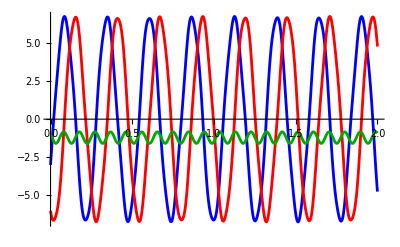

```mathematica
output[t_]:= (S1/.sol[[1]])[t];
Plot[{output[t][[1]],output[t][[2]],output[t][[3]]}, {t,0,2},PlotStyle->{Blue,Red,Darker[Green]}]
```

#### Vector definitions with numerical solution

```mathematica
S1v[t_]:=(S1/.sol[[1]])[t];
S2v[t_]:=(S2/.sol[[1]])[t];
Jv[t_]:=(J/.sol[[1]])[t];
Lv[t_]:=Jv[t]-S1v[t]-S2v[t];
Sv[t_]:=S1v[t]+S2v[t];
```

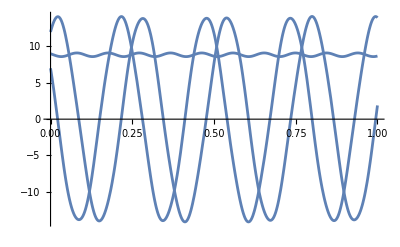

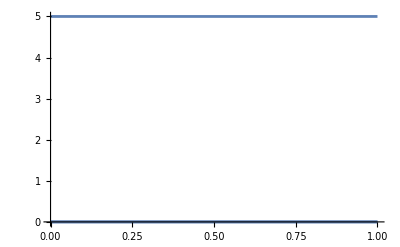

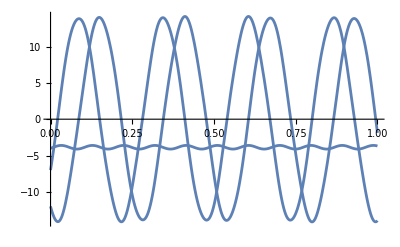

```mathematica
Plot[Lv[t],{t,0,1}]
Plot[Jv[t],{t,0,1}]
Plot[Sv[t],{t,0,1}]
```

#### Vector modulus

```mathematica
NormS1[t_]:=Norm[S1v[t]];
NormS2[t_]:=Norm[S2v[t]];
NormJ[t_]:=Norm[Jv[t]];
NormL[t_]:=Norm[Lv[t]];
NormS[t_]:=Norm[Sv[t]];
```

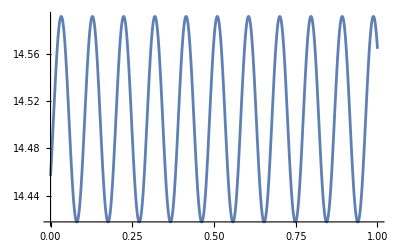

```mathematica
Plot[NormS[t],{t,0,1}]
```

#### Unit vector definitions

```mathematica
S1u[t_]:=S1v[t]/NormS1[t];
Su[t_]:=Sv[t]/NormS[t];
```

#### Cartesian unit vectors test

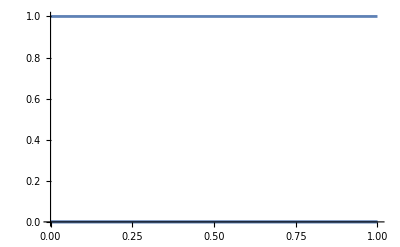

```mathematica
zcapZ[t_]:=Jv[t]/(Jv[t][[3]])
Plot[zcapZ[t],{t,0,1}]
```

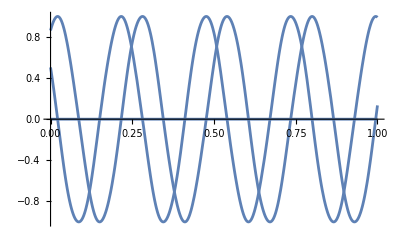

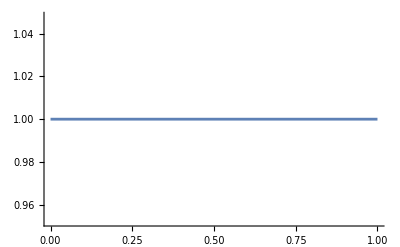

```mathematica
xcapX[t_]:=(Lv[t]-(Dot[Lv[t],zcapZ[t]]zcapZ[t]))/Norm[Lv[t]-(Dot[Lv[t],zcapZ[t]]zcapZ[t])]
Plot[xcapX[t],{t,0,1}]
Plot[Norm[xcapX[t]],{t,0,1}]
```

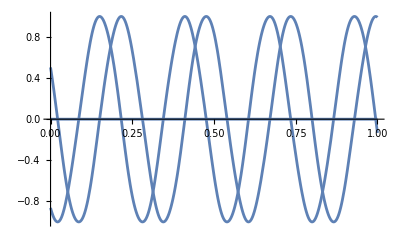

-Graphics-

```mathematica
ycapY[t_]:=Cross[zcapZ[t],xcapX[t]]
Plot[ycapY[t],{t,0,1}]
Plot[Norm[ycapY[t]],{t,0,1}]
```

#### Orthogonal vector definition

```mathematica
SO1[t_]:=Cross[ycapY[t],Sv[t]];
NormSO[t_]:=Norm[SO1[t]];
SOu[t_]:=SO1[t]/NormSO[t]
```

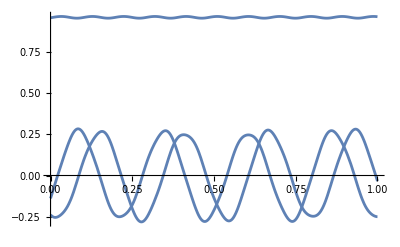

```mathematica
Plot[SOu[t],{t,0,1},PlotRange->All]
```

#### Angle ϕ' definitions

```mathematica
cosϕ1[t_]:=Dot[S1u[t],SOu[t]]/Norm[Cross[S1u[t],Su[t]]];
```

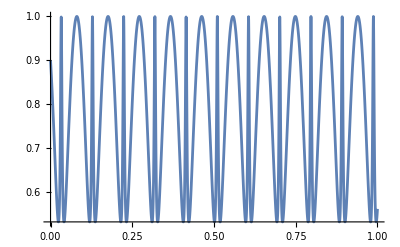

```mathematica
Plot[cosϕ1[t],{t,0,1},PlotRange->All]
```

#### Effective potential ξ (constant of motion) evolution

```mathematica
ξ01[t_]:=Dot[((1+q)S1v[t]+(1+q^-1)S2v[t]),Lv[t]/NormL[t]]
ξ02[t_]:=1/(4 q NormL[t] NormS[t]^2)((-1+q^2) cosϕ1[t] √(NormJ[t]^2-(NormL[t]-NormS[t])^2) √(-NormJ[t]^2+(NormL[t]+NormS[t])^2) √(NormS[t]^2-(NormS1[t]-NormS2[t])^2) √(-NormS[t]^2+(NormS1[t]+NormS2[t])^2)+(NormJ[t]^2-NormL[t]^2-NormS[t]^2) ((1+q)^2 NormS[t]^2+(-1+q^2) (NormS1[t]^2-NormS2[t]^2)))
```

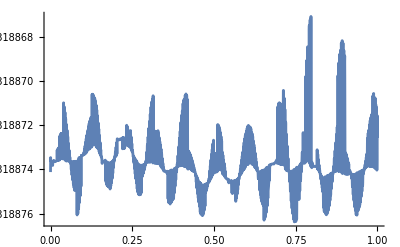

-Graphics-

```mathematica
Plot[ξ01[t],{t,0,1},PlotRange->All]
Plot[ξ02[t],{t,0,1},PlotRange->All]
```

### Test for initial conditions

#### Initial conditions test

```mathematica
S10=N[Norm[{-3,-6,-1}]];
S20=N[Norm[{-4,-6,-3}]];
J0=N[Norm[{0,0,5}] ];
L0=N[Norm[{0,0,5}-{-3,-6,-1}-{-4,-6,-3}]];
S0=N[Norm[{-3,-6,-1}+{-4,-6,-3}]]
```

14.4568

```mathematica
J0>S10+S20-L0
```

True

#### Extremal values of S

```mathematica
rules={J->J0,L->L0,S1->S10,S2->S20};
```

```mathematica
Smin=Max[Abs[J0-L0],Abs[S10-S20]]
Smax=Min[J0+L0,S10+S20]
```

11.5529

14.5926

```mathematica
Abs[S10-S20]
```

1.02792

#### Derivative of ξ_+

```mathematica
dξp=Simplify[-1/(4 L q S^2)(2 (1+q)^2 S^3+2 (1+q)^2 S (-J^2+L^2+S^2)+2 (-1+q^2) S (S1^2-S2^2)-((-1+q^2) √(J^2-(L-S)^2) S √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2))/(√(-S^2+(S1+S2)^2))+((-1+q^2) √(J^2-(L-S)^2) S √(-J^2+(L+S)^2) √(-S^2+(S1+S2)^2))/(√(S^2-(S1-S2)^2))+((-1+q^2) √(J^2-(L-S)^2) (L+S) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2))/(√(-J^2+(L+S)^2))+((-1+q^2) (L-S) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2))/(√(J^2-(L-S)^2)))-((1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2)+(J^2-L^2-S^2) ((1+q)^2 S^2+(-1+q^2) (S1^2-S2^2)))/(2 L q S^3)/.rules]
```

(-449474.+215917. S^2-1.12527×10^-11 S^3-13.0813 S^6+0.0322198 S^8+120.341 √(-249.+33.1059 S-S^2) √(249.+33.1059 S+S^2) √(-225.+214. S^2-1. S^4)+S^4 (9.37721×10^-13-0.128879 √(-249.+33.1059 S-S^2) √(249.+33.1059 S+S^2) √(-225.+214. S^2-1. S^4)))/(S^3 √(-249.+33.1059 S-S^2) √(249.+33.1059 S+S^2) √(-225.+214. S^2-1. S^4))

```mathematica
(* numerator test *)
Solve[(S^3 √(-249.+33.1058907144937 S-S^2) √(249.+33.1058907144937 S+S^2) √(-224.99999999999983+214. S^2-1. S^4))==0,S]
```

{{S→-21.5529},{S→-14.5926},{S→-11.5529},{S→-1.02792},{S→0.},{S→1.02792},{S→11.5529},{S→14.5926},{S→21.5529}}

#### Derivative of ξ_-

```mathematica
dξm=Simplify[1/(4 L q S^2)(-2 (1+q)^2 S^3-2 (1+q)^2 S (-J^2+L^2+S^2)-2 (-1+q^2) S (S1^2-S2^2)+((1-q^2) √(J^2-(L-S)^2) S √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2))/(√(-S^2+(S1+S2)^2))+((-1+q^2) √(J^2-(L-S)^2) S √(-J^2+(L+S)^2) √(-S^2+(S1+S2)^2))/(√(S^2-(S1-S2)^2))+((-1+q^2) √(J^2-(L-S)^2) (L+S) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2))/(√(-J^2+(L+S)^2))+((-1+q^2) (L-S) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2))/(√(J^2-(L-S)^2)))-1/(2 L q S^3)((-1+q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2)+(J^2-L^2-S^2) ((1+q)^2 S^2+(-1+q^2) (S1^2-S2^2)))/.rules]
```

(449474.-215917. S^2+1.12527×10^-11 S^3+13.0813 S^6-0.0322198 S^8+120.341 √(-249.+33.1059 S-S^2) √(249.+33.1059 S+S^2) √(-225.+214. S^2-1. S^4)+S^4 (-9.37721×10^-13-0.128879 √(-249.+33.1059 S-S^2) √(249.+33.1059 S+S^2) √(-225.+214. S^2-1. S^4)))/(S^3 √(-249.+33.1059 S-S^2) √(249.+33.1059 S+S^2) √(-225.+214. S^2-1. S^4))

```mathematica
(* numerator test *)
Solve[(S^3 √(-289.00000000000006+39.44616584663204 S-S^2) √(289.00000000000006+39.44616584663204 S+S^2) √(-224.99999999999983+214. S^2-1. S^4))==0,S]
```

{{S→-29.7231},{S→-14.5926},{S→-9.72308},{S→-1.02792},{S→0.},{S→1.02792},{S→9.72308},{S→14.5926},{S→29.7231}}

#### Boundaries of ξ

```mathematica
ξmax=Simplify[1/(4 L  q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])/.rules/.S->Smin]
```

-25.3387

```mathematica
ξmin=Simplify[1/(4 L  q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])/.rules/.S->Smax]
```

-30.2917

```mathematica
SPlot=Plot[{Callout[NormS[t],Style["ξ=-30.31",20,Blue],Above],Labeled[Smax,Style["ξ_min-30.29",18,Black],Scaled[0.2]],Labeled[Smin,Style["ξ_max-25.34",18,Black],Scaled[0.2]]},{t,0,0.3},PlotRange->All,ImageSize->700,PlotStyle->{{Blue},{Black,Dashed},{Black,Dashed}},Frame->True,FrameLabel->{Style["t",Large,Black],Style["S(t)",Large,Black]},FrameStyle->Directive[Bold,18]]
```

-Graphics-

#### More initial conditions

```mathematica
S1v1={0,7,0};
S2v1={0,7,5};
Jv1={0,0,12};
Sv1=S1v1+S2v1;

nS11=N[Norm[S1v1]];
nS21=N[Norm[S2v1]];
nJ1=N[Norm[Jv1] ];
nL1=N[Norm[Jv1-Sv1-Sv1]];
nS1=N[Norm[S1v1+S2v1]]
nJ1>nS11+nS21-nL1

Smin1=Max[Abs[nJ1-nL1],Abs[nS11-nS21]]
Smax1=Min[nJ1+nL1,nS11+nS21]
```

14.8661

True

16.0713

15.6023

```mathematica
sol1=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]=={4,0,1},S2[0]=={6,0,5}, J[0]=={0,0,5} },   {S1,S2,J},{t,0,30}];
sol2=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]=={0,9,1},S2[0]=={0,5,4}, J[0]=={0,0,5} },   {S1,S2,J},{t,0,30}];
sol3=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]=={0,7,0},S2[0]=={0,7,5}, J[0]=={0,0,12} },   {S1,S2,J},{t,0,30}];
NormSv1[t_]:=Norm[(S1/.sol1[[1]])[t]+(S2/.sol1[[1]])[t]];
NormSv2[t_]:=Norm[(S1/.sol2[[1]])[t]+(S2/.sol2[[1]])[t]];
NormSv3[t_]:=Norm[(S1/.sol3[[1]])[t]+(S2/.sol3[[1]])[t]];
ξ1[t_]:=Dot[((1+q)(S1/.sol1[[1]])[t]+(1+q^-1)(S2/.sol1[[1]])[t]),((J/.sol1[[1]])[t]-(S1/.sol1[[1]])[t]-(S2/.sol1[[1]])[t])/Norm[(J/.sol1[[1]])[t]-(S1/.sol1[[1]])[t]-(S2/.sol1[[1]])[t]]]
ξ2[t_]:=Dot[((1+q)(S1/.sol2[[1]])[t]+(1+q^-1)(S2/.sol2[[1]])[t]),((J/.sol2[[1]])[t]-(S1/.sol2[[1]])[t]-(S2/.sol2[[1]])[t])/Norm[(J/.sol2[[1]])[t]-(S1/.sol2[[1]])[t]-(S2/.sol2[[1]])[t]]]
ξ3[t_]:=Dot[((1+q)(S1/.sol3[[1]])[t]+(1+q^-1)(S2/.sol3[[1]])[t]),((J/.sol3[[1]])[t]-(S1/.sol3[[1]])[t]-(S2/.sol3[[1]])[t])/Norm[(J/.sol3[[1]])[t]-(S1/.sol3[[1]])[t]-(S2/.sol3[[1]])[t]]]
(*Plot[ξ1[t],{t,0,1},PlotRange->All]
Plot[ξ2[t],{t,0,1},PlotRange->All]
Plot[ξ3[t],{t,0,1},PlotRange->All]*)
```

```mathematica
Show[SPlot,Plot[Callout[NormSv1[t],Style["ξ=-23.78",20,Red],Below],{t,0,0.3},PlotStyle->Red],Plot[Callout[NormSv2[t],Style["ξ=-27.73",20,Darker[Green]],Below],{t,0,0.3},PlotStyle->Darker[Green]],Plot[Callout[NormSv3[t],Style["ξ=-20.75",20,Purple],Below],{t,0,0.3},PlotStyle->Purple],PlotRange->{{0,0.3},{10,15}},ImageSize->700,ImageResolution->700]
```

-Graphics-

#### Region Plot for ξ vs S

```mathematica
ContξS=Simplify[1/(4 L  q S^2)((J^2-L^2-S^2) ((1+q)^2 S^2-(1-q^2) (S1^2-S2^2))-(1-q^2) √(J^2-(L-S)^2) √(-J^2+(L+S)^2) √(S^2-(S1-S2)^2) √(-S^2+(S1+S2)^2) Cos[ϕ])/.rules/.Cos[ϕ]->+1]
```

(-60.1706-16.2871 S^2-0.0644397 S^4-0.0161099 √(-249.+33.1059 S-S^2) √(249.+33.1059 S+S^2) √(-225.+214. S^2-1. S^4))/S^2

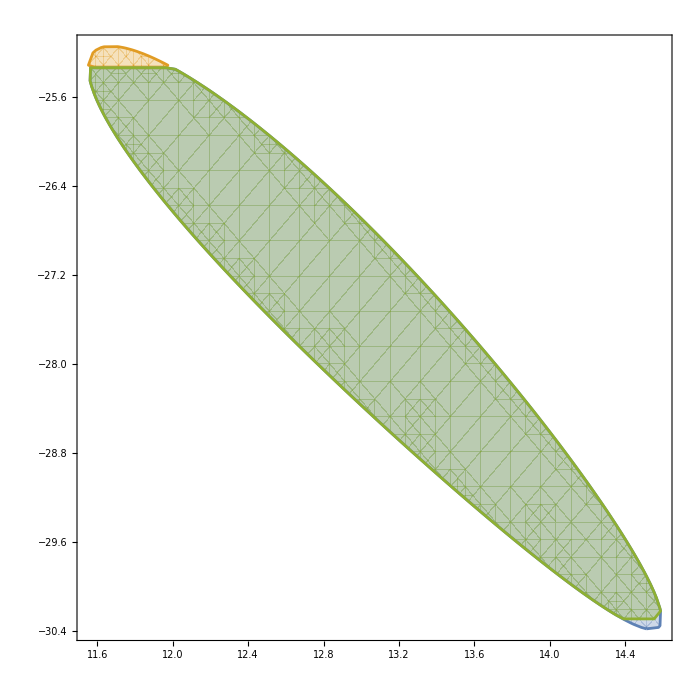

```mathematica
RegionPlot[{ξ<(-60.17056049568562-16.287131636181577 S^2-0.0644396899552189 S^4+0.01610992248880472 √(-249.+33.1058907144937 S-S^2) √(249.+33.1058907144937 S+S^2) √(-224.99999999999983+214. S^2-1. S^4))/S^2&&ξ>(-60.17056049568562-16.287131636181577 S^2-0.0644396899552189 S^4-0.01610992248880472 √(-249.+33.1058907144937 S-S^2) √(249.+33.1058907144937 S+S^2) √(-224.99999999999983+214. S^2-1. S^4))/S^2&&ξ<ξmax,ξ<(-60.17056049568562-16.287131636181577 S^2-0.0644396899552189 S^4+0.01610992248880472 √(-249.+33.1058907144937 S-S^2) √(249.+33.1058907144937 S+S^2) √(-224.99999999999983+214. S^2-1. S^4))/S^2&&ξ>(-60.17056049568562-16.287131636181577 S^2-0.0644396899552189 S^4-0.01610992248880472 √(-249.+33.1058907144937 S-S^2) √(249.+33.1058907144937 S+S^2) √(-224.99999999999983+214. S^2-1. S^4))/S^2&&ξmax<ξ,ξ<(-60.17056049568562-16.287131636181577 S^2-0.0644396899552189 S^4+0.01610992248880472 √(-249.+33.1058907144937 S-S^2) √(249.+33.1058907144937 S+S^2) √(-224.99999999999983+214. S^2-1. S^4))/S^2&&ξ>(-60.17056049568562-16.287131636181577 S^2-0.0644396899552189 S^4-0.01610992248880472 √(-249.+33.1058907144937 S-S^2) √(249.+33.1058907144937 S+S^2) √(-224.99999999999983+214. S^2-1. S^4))/S^2&&ξmin<ξ<ξmax},{S,Smin,Smax},{ξ,-31,-25},PlotRange->All,ImageSize->700]
```

-Graphics-

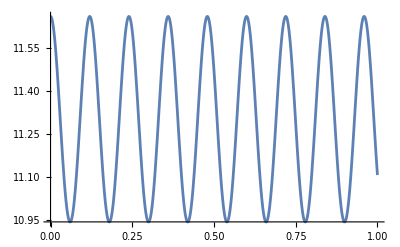

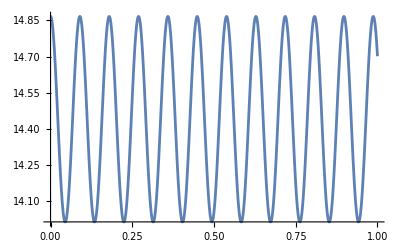

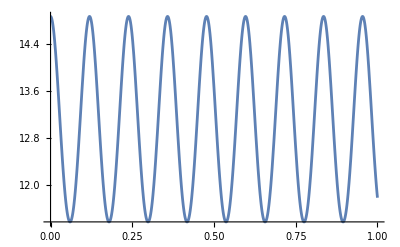

```mathematica
Plot[NormS[t],{t,0,1}]
Plot[NormSv1[t],{t,0,1}]
Plot[NormSv2[t],{t,0,1}]
Plot[NormSv3[t],{t,0,1}]
```